Final population using forward Euler is 102.504

Final population using midpoint is 102.711

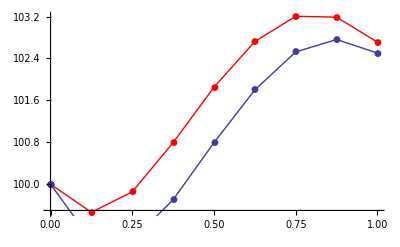

Forward Euler in blue and midpoint in red

```mathematica
Clear[t,B,i,Δt,n]
Δt=.125;
Subscript[t, 0]=0;
u[Subscript[t, 0]]=100.;
i=0;
n=1;
fePoints={{Subscript[t, 0],u[Subscript[t, 0]]}};
mPoints={{Subscript[t, 0],u[Subscript[t, 0]]}};
B={.007,.0036,.0011,.0001,.0004,.0013,.0028,.0043,.0056};
(*Get the  points using Forward Euler*)
While[i<9,
	Subscript[t, i+1]=Subscript[t, i]+Δt;
	u'[Subscript[t, i]]=.09*u[Subscript[t, i]]-B[[i+1]]*u[Subscript[t, i]]^1.7;
	u[Subscript[t, i+1]]=u[Subscript[t, i]]+(u'[Subscript[t, i]])*(Δt);
	population={Subscript[t, i],u[Subscript[t, i]]};
	AppendTo[fePoints,population];
	Subscript[t, i]=Subscript[t, i+1];
	i++];
Print["Final population using forward Euler is ",population[[2]]]
fePlot =ListLinePlot[fePoints,PlotMarkers->Automatic];
(*Get the points using midpoint method*)
Subscript[u, 0]=100.;
Subscript[u, p]=.09*Subscript[u, 0]-(B[[1]]*(Subscript[u, 0])^1.7);
AppendTo[mPoints,{0,Subscript[u, 0]}];
While[n<9,
	Subscript[u, pn]=.09*(Subscript[u, 0]+Subscript[u, p]*Δt)-B[[n+1]]*(Subscript[u, 0]+Subscript[u, p]*Δt)^1.7;
	Subscript[u, n]=Subscript[u, 0]+(Subscript[u, p]+Subscript[u, pn])/2*Δt;
	Subscript[u, 0]=Subscript[u, n];
	Subscript[u, p]=Subscript[u, pn];
	AppendTo[mPoints,{n*Δt,Subscript[u, n]}];
	finalPopulation=Subscript[u, n];
	n++
	];
mPlot=ListLinePlot[mPoints, PlotMarkers->Automatic,PlotStyle->{Red}];
Print["Final population using midpoint is ",finalPopulation]
Show[mPlot,fePlot]
Print["Forward Euler in blue and midpoint in red"]
```